```mathematica
Y[s_,l_,m_,θ_,ϕ_]:=(-1)^m Simplify[√(((l+m)!(l-m)!(2l+1))/((l+s)!(l-s)!4π))(Sin[θ/2])^(2l)∑_(r=0)^(l-s) (Binomial[l-s,r]Binomial[l+s,r+s-m](-1)^(l-r-s)ⅇ^(ⅈ m ϕ)(Cot[θ/2])^(2r+s-m)),Assumptions->{ϕ∈Reals,θ∈Reals}]
```

```mathematica
TE2a[l_,m_,θ_,ϕ_]:= 1/2^1.5(Y[-2,l,m,θ,ϕ] + Y[2,l,m,θ,ϕ])
TB2a[l_,m_,θ_,ϕ_]:= 1/2^1.5(Y[-2,l,m,θ,ϕ] - Y[2,l,m,θ,ϕ])
TE2b[l_,m_,θ_,ϕ_]:=ⅈ/2^1.5(Y[-2,l,m,θ,ϕ] - Y[2,l,m,θ,ϕ])
TB2b[l_,m_,θ_,ϕ_]:=ⅈ/2^1.5(Y[-2,l,m,θ,ϕ] + Y[2,l,m,θ,ϕ])
TE2[l_,m_,θ_,ϕ_]:={{TE2a[l,m,θ,ϕ],TE2b[l,m,θ,ϕ]}, {TE2b[l,m,θ,ϕ], -TE2a[l,m,θ,ϕ]}}
TB2[l_,m_,θ_,ϕ_]:={{TB2a[l,m,θ,ϕ],TB2b[l,m,θ,ϕ]}, {TB2b[l,m,θ,ϕ], -TB2a[l,m,θ,ϕ]}}
mom[t_,r_,M_,Ω_,ω_,l_]:=-M ⅇ^(-ⅈ (Ω (t-r)+ω))
EMas[θ_,ϕ_,w_]=mom[0, 1, 1, 1, w, 0]TE2[2,2,θ,ϕ];
ECur[θ_,ϕ_,w_]=mom[0, 1, 1, 1, w, 0]TB2[2,2,θ,ϕ];
```

```mathematica
TestEigenM[θ_,ϕ_,w_]:=Max[Eigenvalues[Refine[ComplexExpand[Re[EMas[θ,ϕ,w]]],{θ,ϕ}∈Reals]]]
TestEigenC[θ_,ϕ_,w_]:=Max[Eigenvalues[Refine[ComplexExpand[Re[ECur[θ,ϕ,w]]],{θ,ϕ}∈Reals]]]
TestEigenS[θ_,ϕ_,w_]:=Max[Eigenvalues[Refine[ComplexExpand[Re[EMas[θ,ϕ,0]+ECur[θ,ϕ,w]]],{θ,ϕ}∈Reals]]]
```

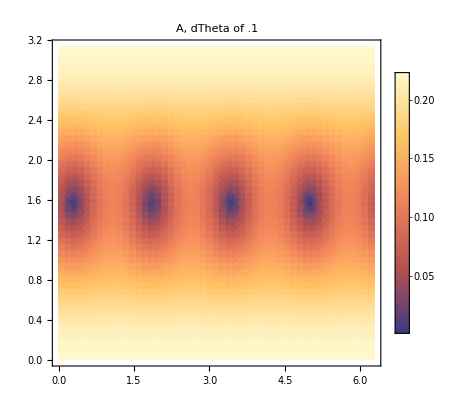

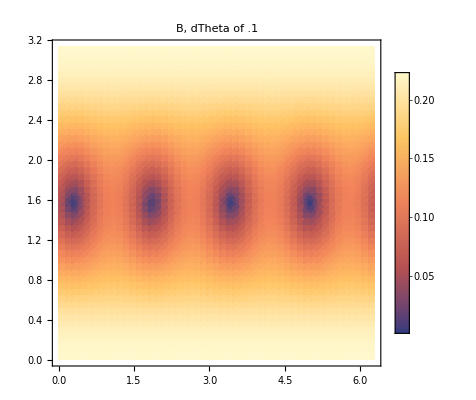

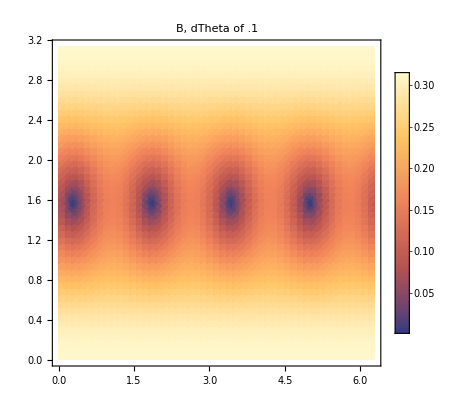

```mathematica
DensityPlot[TestEigenM[θ,ϕ,0], {ϕ, 0, 2*Pi},{θ, 0, Pi},PlotLegends->Automatic, PlotLabel->"A, dTheta of .1",PlotPoints->50]
DensityPlot[TestEigenC[θ,ϕ,Pi/2], {ϕ, 0, 2*Pi},{θ, 0, Pi},PlotLegends->Automatic, PlotLabel->"B, dTheta of .1",PlotPoints->50]
DensityPlot[TestEigenS[θ,ϕ,Pi/2], {ϕ, 0, 2*Pi},{θ, 0, Pi},PlotLegends->Automatic, PlotLabel->"B, dTheta of .1",PlotPoints->50]
```